```mathematica
A=S;
B=-ConjugateTranspose[minusSstar];
U=RandomReal[{-1,1},Length[massU]];
Q=RandomReal[{-1,1},Length[massQ]];
λ=RandomReal[{-1,1},Length[Γ]];
μ=RandomReal[{-1,1},Length[Ξ]];
f=massQ.Q+A.U+ConjugateTranspose[Ξ].μ;
g=-ConjugateTranspose[B].Q+ConjugateTranspose[Γ].λ;
h=Ξ.Q;
j=Γ.U;
u0=RandomReal[{-1,1},Length[U]];
(*u0=U;*)

uNow=(u0-ConjugateTranspose[Γ].LinearSolve[Γ.ConjugateTranspose[Γ],Γ.u0])+ConjugateTranspose[Γ].LinearSolve[Γ.ConjugateTranspose[Γ],j];
uTildeNow=uNow-U;
Δt=0.001;
```

```mathematica
-Γ.Inverse[ConjugateTranspose[B].inverseMassQ.A].ConjugateTranspose[B].Q+Γ.Inverse[ConjugateTranspose[B].inverseMassQ.A].ConjugateTranspose[Γ].λ-Γ.Inverse[ConjugateTranspose[B].inverseMassQ.A].g
```

```mathematica
Inverse[Γ.Inverse[ConjugateTranspose[B].inverseMassQ.A].ConjugateTranspose[Γ]].(-Γ.Inverse[ConjugateTranspose[B].inverseMassQ.A].ConjugateTranspose[B].Q-Γ.Inverse[ConjugateTranspose[B].inverseMassQ.A].g)+λ
```

```mathematica
+Inverse[Γ.Inverse[ConjugateTranspose[B].inverseMassQ.A].ConjugateTranspose[Γ]].Γ.Inverse[ConjugateTranspose[B].inverseMassQ.A].ConjugateTranspose[B].Q+Inverse[Γ.Inverse[ConjugateTranspose[B].inverseMassQ.A].ConjugateTranspose[Γ]].Γ.Inverse[ConjugateTranspose[B].inverseMassQ.A].g
```

{-0.308178,0.149053,-0.00187407,-0.590742,0.384071,-0.987326}

```mathematica
-(ℐ-ℙ).ConjugateTranspose[B].Q-(ℐ-ℙ).g//Chop
```

{0,0,0,0,0,0,0,0,0}

```mathematica
(ℐ-ℙ).ConjugateTranspose[B].inverseMassQ.f+(ℐ-ℙ).g-(ℐ-ℙ).ConjugateTranspose[B].inverseMassQ.A.U-(ℐ-ℙ).ConjugateTranspose[B].inverseMassQ.ConjugateTranspose[Ξ].μ//Chop
```

{0,0,0,0,0,0,0,0,0}

```mathematica
λ
```

{-0.308178,0.149053,-0.00187407,-0.590742,0.384071,-0.987326}

```mathematica
λ
```

{-0.308178,0.149053,-0.00187407,-0.590742,0.384071,-0.987326}

```mathematica
ℙ=ConjugateTranspose[Γ].Inverse[Γ.Inverse[ConjugateTranspose[B].inverseMassQ.A].ConjugateTranspose[Γ]].Γ.Inverse[ConjugateTranspose[B].inverseMassQ.A]
```

```mathematica
ℐ=IdentityMatrix[Length[ℙ]];
```

```mathematica
LinearSolve[(ConjugateTranspose[B].inverseMassQ.A),((ℐ-ℙ).(ConjugateTranspose[B].inverseMassQ.f+g)+ConjugateTranspose[Γ].Inverse[Γ.Inverse[ConjugateTranspose[B].inverseMassQ.A].ConjugateTranspose[Γ]].j)
]-U//Chop
```

{0,0.4102,0,0,0.19502,0,0,-0.0615019,0}

```mathematica
U
```

{-0.402073,0.306281,0.196277,0.351962,-0.165915,-0.137765,0.177337,0.924362,-0.0387419}

```mathematica
x
```

```mathematica
ConjugateTranspose[Γ].Inverse[Γ.Inverse[ConjugateTranspose[B].inverseMassQ.A].ConjugateTranspose[Γ]].j
```

{-0.450613,0.,0.24973,0.997035,0.,-0.192657,0.265703,0.,0.00144364}

Dot::dotsh: Tensors {{1.34214, 0., -0.266272, 0.503683, 0., -0.0739728, -0.25207, 0., 0.0381256}, « 7 », {0.0381256, 0., -0.168406, « 3 », -0.123899, 0., 0.558383}} and {-0.226552, 1.0853, 0.380205, 0.11484, -0.395667, -0.131272} have incompatible shapes.

{{1.34214,0.,-0.266272,0.503683,0.,-0.0739728,-0.25207,0.,0.0381256},{0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.266272,0.,1.02025,-0.0739728,0.,0.32542,0.0381256,0.,-0.168406},{0.503683,0.,-0.0739728,3.34852,0.,-0.29817,-0.00337966,0.,0.128009},{0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0739728,0.,0.32542,-0.29817,0.,1.57974,0.128009,0.,-0.351158},{-0.25207,0.,0.0381256,-0.00337966,0.,0.128009,0.963669,0.,-0.123899},{0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0381256,0.,-0.168406,0.128009,0.,-0.351158,-0.123899,0.,0.558383}}.{-0.226552,1.0853,0.380205,0.11484,-0.395667,-0.131272}

{{1.,-0.148667,1.61329×10^-16,6.89553×10^-17,-0.00273411,-2.42861×10^-17,-1.35308×10^-16,0.00341763,5.55112×10^-17},{0.,0.,0.,0.,0.,0.,0.,0.,0.},{-1.73472×10^-18,-0.00666439,1.,1.56125×10^-17,0.0136705,4.16334×10^-17,4.16334×10^-17,-0.0170882,5.55112×10^-17},{-2.42861×10^-16,0.000341763,-1.66533×10^-16,1.,-0.199419,7.63278×10^-17,-3.46945×10^-16,-0.0632262,-3.33067×10^-16},{0.,0.,0.,0.,0.,0.,0.,0.,0.},{-4.16334×10^-17,-0.00170882,1.94289×10^-16,4.85723×10^-17,0.247095,1.,-5.55112×10^-17,0.316131,-3.33067×10^-16},{-1.31839×10^-16,0.00367396,-6.93889×10^-18,9.36751×10^-17,-0.0187543,-6.93889×10^-18,1.,-0.179682,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,-0.0183698,-1.11022×10^-16,-3.1225×10^-17,0.0937714,2.77556×10^-17,8.32667×10^-17,0.148411,1.}}

{{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0}}

```mathematica
zzz=SparseArray@ArrayFlatten[
{
{ConjugateTranspose[B].inverseMassQ.A,ConjugateTranspose[B].inverseMassQ.ConjugateTranspose[Ξ],ConjugateTranspose[Γ]},
{Ξ.inverseMassQ.A,Ξ.inverseMassQ.ConjugateTranspose[Ξ],0},
{Γ,0,0}
}
]
```

```mathematica
Γ.LinearSolve[ConjugateTranspose[B].inverseMassQ.A,ConjugateTranspose[Γ].λ]+Γ.LinearSolve[ConjugateTranspose[B].inverseMassQ.A,ConjugateTranspose[B].inverseMassQ.ConjugateTranspose[Ξ].μ]-(Γ.LinearSolve[ConjugateTranspose[B].inverseMassQ.A,ConjugateTranspose[B].inverseMassQ.f+g]-j)//Chop
```

```mathematica
Ξ.inverseMassQ.A.LinearSolve[ConjugateTranspose[B].inverseMassQ.A,ConjugateTranspose[B].inverseMassQ.ConjugateTranspose[Ξ].μ]-Ξ.inverseMassQ.ConjugateTranspose[Ξ].μ+Ξ.inverseMassQ.A.LinearSolve[ConjugateTranspose[B].inverseMassQ.A,ConjugateTranspose[Γ].λ]-(Ξ.inverseMassQ.A.LinearSolve[ConjugateTranspose[B].inverseMassQ.A,ConjugateTranspose[B].inverseMassQ.f]-Ξ.inverseMassQ.f+Ξ.inverseMassQ.A.LinearSolve[ConjugateTranspose[B].inverseMassQ.A,g]+h)
```

```mathematica
BB=SparseArray@(Ξ.inverseMassQ.A.LinearSolve[ConjugateTranspose[B].inverseMassQ.A,ConjugateTranspose[B].inverseMassQ.ConjugateTranspose[Ξ]]-Ξ.inverseMassQ.ConjugateTranspose[Ξ])
BA=SparseArray@(Ξ.inverseMassQ.A.LinearSolve[ConjugateTranspose[B].inverseMassQ.A,ConjugateTranspose[Γ]])
AA=SparseArray@(Γ.LinearSolve[ConjugateTranspose[B].inverseMassQ.A,ConjugateTranspose[Γ]])
AB=SparseArray@(Γ.LinearSolve[ConjugateTranspose[B].inverseMassQ.A,ConjugateTranspose[B].inverseMassQ.ConjugateTranspose[Ξ]])
```

{-1.33227×10^-15,-8.88178×10^-16,-6.66134×10^-16,-1.16573×10^-15,8.43769×10^-15,4.44089×10^-16}

```mathematica
FF=(Γ.LinearSolve[ConjugateTranspose[B].inverseMassQ.A,ConjugateTranspose[B].inverseMassQ.f+g]-j);
GG=(Ξ.inverseMassQ.A.LinearSolve[ConjugateTranspose[B].inverseMassQ.A,ConjugateTranspose[B].inverseMassQ.f]-Ξ.inverseMassQ.f+Ξ.inverseMassQ.A.LinearSolve[ConjugateTranspose[B].inverseMassQ.A,g]+h);AA.λ+AB.μ-FF
BA.λ+BB.μ-GG
```

```mathematica
(BA.λ+BA.Inverse[AA].AB.μ-BA.Inverse[AA].FF)-(BA.λ+BB.μ-GG)
(BA.Inverse[AA].AB.μ-BA.Inverse[AA].FF)-BB.μ+GG
```

```mathematica
LinearSolve[BA.Inverse[AA].AB-BB,-GG+BA.Inverse[AA].FF]
```

```mathematica
μ
```

{0.966218,-0.380188,-0.239882,0.176334,-0.242857,-0.406848}

```mathematica
Γ.LinearSolve[ConjugateTranspose[B].inverseMassQ.A,ConjugateTranspose[Γ]]
```

{{0.557832,0.354887,-0.168734,0.143958,0.0786326,-0.0429455},{0.354887,3.57849,0.770067,0.0786326,0.474215,0.0205655},{-0.168734,0.770067,0.799537,-0.0429455,0.0205655,0.129441},{0.143958,0.0786326,-0.0429455,0.744228,0.594705,-0.210252},{0.0786326,0.474215,0.0205655,0.594705,10.003,3.13514},{-0.0429455,0.0205655,0.129441,-0.210252,3.13514,1.95275}}

```mathematica
BA.λ+BA.LinearSolve[AA,AB.μ]-
```

{0.398836,-0.28344,-0.36331,-0.0305034,-0.160259,-0.280197}

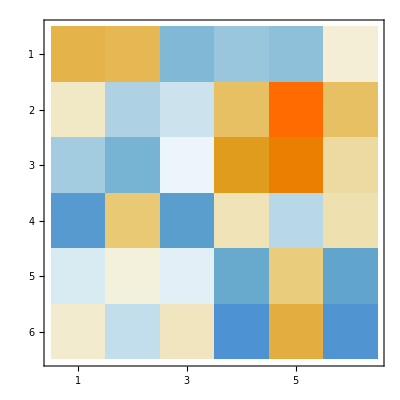

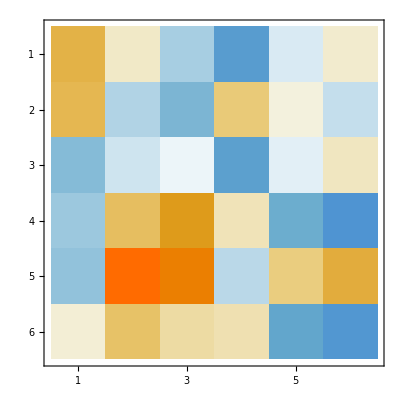

```mathematica
BA//MatrixPlot
AB//MatrixPlot
```

```mathematica
SingularValueList[AA]
```

{11.1332,3.78205,1.27712,0.733446,0.448966,0.261065}

{0.0982381,-0.340383,-0.410518,-0.0243028,0.231125,0.539661}

{0.8584,-1.85992,-0.983711,-0.598421,-2.63487,0.253071}

{0.481968,-0.490196,-0.659085,0.527483,2.8626,-0.233126}

{0.705204,-0.490285,-0.558965,-0.0585776,0.204141,0.483356}

{0.99057,3.93711,0.619467,-0.360314,-3.01255,-1.10588}

{0.398156,0.516823,-0.105151,-0.190159,-1.22814,0.01464}

```mathematica
SingularValueList[zzz]
```

21

```mathematica
A+B
```

SparseArray[<144>, {18, 9}]

## Iterative Heat Equation-Like

```mathematica
μNow=LinearSolve[Ξ.inverseMassQ.ConjugateTranspose[Ξ],Ξ.inverseMassQ.(f-S.uNow)-h];
μTildeNow=μNow-μ;
QNow=LinearSolve[massQ,f-S.uNow-ConjugateTranspose[Ξ].μNow];
QTildeNow=QNow-Q;

λNow=LinearSolve[Γ.inverseMassU.ConjugateTranspose[Γ],Γ.inverseMassU.(g+ConjugateTranspose[S].QNow)];
λTildeNow=λNow-λ;
λTildeNow=LinearSolve[Γ.inverseMassU.ConjugateTranspose[Γ],Γ.inverseMassU.(ConjugateTranspose[S].QTildeNow)];
uDotNow=inverseMassU.(g+ConjugateTranspose[S].QNow-ConjugateTranspose[Γ].λNow);
uNext=uNow+Δt uDotNow;
uTildeNext=uNext-U;
uTildeDotNow=(uTildeNext-uTildeNow)/Δt;
Norm[uTildeNext];
ℐ=SparseArray@IdentityMatrix@Length@Dot[ConjugateTranspose[S].QTildeNow];
ℙ=(ℐ-ConjugateTranspose[Γ].SparseArray[Inverse[Γ.inverseMassU.ConjugateTranspose[Γ]]].Γ.inverseMassU);
```

```mathematica
AA=
SparseArray@ArrayFlatten[
{
{0massQ,S,ConjugateTranspose[Ξ],0},
{-ConjugateTranspose[S],0,0,ConjugateTranspose[Γ]},
{Ξ,0,0,0},
{0,Γ,0,0}
}
]
BB=SparseArray@ArrayFlatten[
{
{ⅈ massQ,0S,0 ConjugateTranspose[Ξ],0},
{-0 ConjugateTranspose[S],ⅈ massU,0,0 ConjugateTranspose[Γ]},
{0Ξ,0,0,0},
{0,0Γ,0,0}
}
]
```

SparseArray[<24624>, {279, 279}]

SparseArray[<19683>, {279, 279}]

```mathematica
massQ.Q+S.U+ConjugateTranspose[Ξ].μ-f//Norm
-ConjugateTranspose[S].Q+ConjugateTranspose[Γ].λ-g//Norm
Ξ.Q-h//Norm
Γ.U-j//Norm
massQ.QNow+S.uNow+ConjugateTranspose[Ξ].μNow-f//Norm
-ConjugateTranspose[S].QNow+massU.uDotNow+ConjugateTranspose[Γ].λNow-g//Norm
```

0.

1.95475×10^-15

0.

0.

2.53052×10^-13

1.54993×10^-10

```mathematica
massQ.QTildeNow+S.uTildeNow+ConjugateTranspose[Ξ].μTildeNow//Norm
-ConjugateTranspose[S].QTildeNow+massU.uTildeDotNow+ ConjugateTranspose[Γ].λTildeNow//Norm
Ξ.QTildeNow//Norm
Γ.uTildeNow//Norm
```

2.68922×10^-13

1.72572×10^-10

5.20998×10^-12

2.79148×10^-14

```mathematica
Dot[QTildeNow,massQ.QTildeNow]+Dot[QTildeNow,S.((uTildeNow+uTildeNext)/2)]-Δt/2 Dot[QTildeNow,S. ((uTildeNext-uTildeNow)/Δt)]+Dot[QTildeNow,ConjugateTranspose[Ξ].μTildeNow]+Dot[(uTildeNext+uTildeNow)/2,-ConjugateTranspose[S].QTildeNow]+ Dot[(uTildeNext+uTildeNow)/2,massU.uTildeDotNow]+ Dot[(uTildeNext+uTildeNow)/2,ConjugateTranspose[Γ].μTildeNow]
Dot[QTildeNow,massQ.QTildeNow]+0Dot[QTildeNow,S.((uTildeNow+uTildeNext)/2)]-Δt/2 Dot[QTildeNow,S. ((uTildeNext-uTildeNow)/Δt)]+0Dot[QTildeNow,ConjugateTranspose[Ξ].μTildeNow]+0Dot[(uTildeNext+uTildeNow)/2,-ConjugateTranspose[S].QTildeNow]+ Dot[(uTildeNext+uTildeNow)/2,massU.uTildeDotNow]+ 0Dot[(uTildeNext+uTildeNow)/2,ConjugateTranspose[Γ].μTildeNow]
Dot[QTildeNow,massQ.QTildeNow]+-Δt/2 Dot[ConjugateTranspose[S].QTildeNow, (uTildeNext-uTildeNow)/Δt]+ Dot[(uTildeNext+uTildeNow)/2,massU.uTildeDotNow]
Dot[QTildeNow,massQ.QTildeNow]+-Δt/2 Dot[ConjugateTranspose[S].QTildeNow, (uTildeNext-uTildeNow)/Δt]+ Dot[(uTildeNext+uTildeNow)/2,massU.((uTildeNext-uTildeNow)/Δt)]
Dot[QTildeNow,massQ.QTildeNow]+-Δt/2 Dot[ConjugateTranspose[S].QTildeNow, (uTildeNext-uTildeNow)/Δt]+ Dot[(uTildeNext+uTildeNow)/2,massU.((uTildeNext-uTildeNow)/Δt)]
1/(2Δt)(Dot[uTildeNext,massU.uTildeNext]-Dot[uTildeNow,massU.uTildeNow])+Dot[QTildeNow,massQ.QTildeNow]+-Δt/2 Dot[ConjugateTranspose[S].QTildeNow, (uTildeNext-uTildeNow)/Δt]+Δt/2 Dot[(uTildeNext-uTildeNext)/Δt,massU.((uTildeNext-uTildeNext)/Δt)]-Δt/2 Dot[(uTildeNext-uTildeNext)/Δt,massU.((uTildeNext-uTildeNext)/Δt)]+Δt/2 Dot[(uTildeNext-uTildeNext)/Δt,ConjugateTranspose[Γ].λTildeNow]+ Δt/2 Dot[(uTildeNext-uTildeNext)/Δt,ConjugateTranspose[Γ].λTildeNow]
1/(2Δt)(Dot[uTildeNext,massU.uTildeNext]-Dot[uTildeNow,massU.uTildeNow])+Dot[QTildeNow,massQ.QTildeNow]-0 Δt/2 Dot[ConjugateTranspose[S].QTildeNow, (uTildeNext-uTildeNow)/Δt]+0 Δt/2 Dot[(uTildeNext-uTildeNow)/Δt,massU.((uTildeNext-uTildeNow)/Δt)]-Δt/2 Dot[(uTildeNext-uTildeNow)/Δt,massU.((uTildeNext-uTildeNow)/Δt)]+0 Δt/2 Dot[(uTildeNext-uTildeNow)/Δt,ConjugateTranspose[Γ].λTildeNow]-Δt/2 Dot[(uTildeNext-uTildeNow)/Δt,ConjugateTranspose[Γ].λTildeNow]
1/(2Δt)(Dot[uTildeNext,massU.uTildeNext]-Dot[uTildeNow,massU.uTildeNow])+Dot[QTildeNow,massQ.QTildeNow]-Δt/2 Dot[(uTildeNext-uTildeNow)/Δt,massU.((uTildeNext-uTildeNow)/Δt)]-Δt/2 Dot[(uTildeNext-uTildeNow)/Δt,ConjugateTranspose[Γ].λTildeNow]
1/(2Δt)(Dot[uTildeNext,massU.uTildeNext]-Dot[uTildeNow,massU.uTildeNow])+Dot[QTildeNow,massQ.QTildeNow]-Δt/2 Dot[(uTildeNext-uTildeNow)/Δt,massU.((uTildeNext-uTildeNow)/Δt)]-Δt/2 Dot[Γ.((uTildeNext-uTildeNow)/Δt),λTildeNow]
1/(2Δt)(Dot[uTildeNext,massU.uTildeNext]-Dot[uTildeNow,massU.uTildeNow])+Dot[QTildeNow,massQ.QTildeNow]-Δt/2 Dot[inverseMassU.(ConjugateTranspose[S].QTildeNow-ConjugateTranspose[Γ].λTildeNow),massU.(inverseMassU.(ConjugateTranspose[S].QTildeNow-ConjugateTranspose[Γ].λTildeNow))]
1/(2Δt)(Dot[uTildeNext,massU.uTildeNext]-Dot[uTildeNow,massU.uTildeNow])+Dot[QTildeNow,massQ.QTildeNow]-Δt/2 Dot[inverseMassU.(ConjugateTranspose[S].QTildeNow-0 ConjugateTranspose[Γ].λTildeNow),massU.(inverseMassU.(ConjugateTranspose[S].QTildeNow-0 ConjugateTranspose[Γ].λTildeNow))]-Δt/2 Dot[inverseMassU.(ConjugateTranspose[S].QTildeNow-0 ConjugateTranspose[Γ].λTildeNow),massU.(inverseMassU.(0 ConjugateTranspose[S].QTildeNow-ConjugateTranspose[Γ].λTildeNow))]-Δt/2 Dot[inverseMassU.(0 ConjugateTranspose[S].QTildeNow-ConjugateTranspose[Γ].λTildeNow),massU.(inverseMassU.(ConjugateTranspose[S].QTildeNow-0 ConjugateTranspose[Γ].λTildeNow))]-Δt/2 Dot[inverseMassU.(0 ConjugateTranspose[S].QTildeNow-ConjugateTranspose[Γ].λTildeNow),massU.(inverseMassU.(0 ConjugateTranspose[S].QTildeNow-ConjugateTranspose[Γ].λTildeNow))]
1/(2Δt)(Dot[uTildeNext,massU.uTildeNext]-Dot[uTildeNow,massU.uTildeNow])+Dot[QTildeNow,massQ.QTildeNow]-Δt/2 Dot[inverseMassU.(ConjugateTranspose[S].QTildeNow),massU.(inverseMassU.(ConjugateTranspose[S].QTildeNow))]+2 Δt/2 Dot[inverseMassU.(ConjugateTranspose[S].QTildeNow),massU.(inverseMassU.(ConjugateTranspose[Γ].λTildeNow))]+-Δt/2 Dot[inverseMassU.(ConjugateTranspose[Γ].λTildeNow),massU.(inverseMassU.(ConjugateTranspose[Γ].λTildeNow))]
1/(2Δt)(Dot[uTildeNext,massU.uTildeNext]-Dot[uTildeNow,massU.uTildeNow])+Dot[QTildeNow,massQ.QTildeNow]-Δt/2 Dot[inverseMassU.(ConjugateTranspose[S].QTildeNow),massU.(inverseMassU.(ConjugateTranspose[S].QTildeNow))]+Δt/2 Dot[inverseMassU.(ConjugateTranspose[Γ].(LinearSolve[Γ.inverseMassU.ConjugateTranspose[Γ],Γ.inverseMassU.(ConjugateTranspose[S].QTildeNow)])),massU.(inverseMassU.(ConjugateTranspose[Γ].(LinearSolve[Γ.inverseMassU.ConjugateTranspose[Γ],Γ.inverseMassU.(ConjugateTranspose[S].QTildeNow)])))]
1/(2Δt)(Dot[uTildeNext,massU.uTildeNext]-Dot[uTildeNow,massU.uTildeNow])+Dot[QTildeNow,massQ.QTildeNow]-Δt/2 Dot[inverseMassU.(ConjugateTranspose[S].QTildeNow),massU.inverseMassU.(ConjugateTranspose[S].QTildeNow)]+Δt/2 Dot[inverseMassU.(ConjugateTranspose[Γ].(LinearSolve[Γ.inverseMassU.ConjugateTranspose[Γ],Γ.inverseMassU.ConjugateTranspose[S].QTildeNow])),(ConjugateTranspose[Γ].(LinearSolve[Γ.inverseMassU.ConjugateTranspose[Γ],Γ.inverseMassU.ConjugateTranspose[S].QTildeNow]))]
1/(2Δt)(Dot[uTildeNext,massU.uTildeNext]-Dot[uTildeNow,massU.uTildeNow])+Dot[QTildeNow,massQ.QTildeNow]-Δt/2 Dot[inverseMassU.(ConjugateTranspose[S].QTildeNow),(ConjugateTranspose[S].QTildeNow)]+Δt/2 Dot[inverseMassU.(ConjugateTranspose[Γ].(LinearSolve[Γ.inverseMassU.ConjugateTranspose[Γ],Γ.inverseMassU.ConjugateTranspose[S].QTildeNow])),(ConjugateTranspose[Γ].(LinearSolve[Γ.inverseMassU.ConjugateTranspose[Γ],Γ.inverseMassU.ConjugateTranspose[S].QTildeNow]))]
1/(2Δt)(Dot[uTildeNext,massU.uTildeNext]-Dot[uTildeNow,massU.uTildeNow])+Dot[QTildeNow,massQ.QTildeNow]-Δt/2 Dot[QTildeNow,(S.inverseMassU.ConjugateTranspose[S].QTildeNow)]+Δt/2 Dot[((LinearSolve[Γ.inverseMassU.ConjugateTranspose[Γ],Γ.inverseMassU.ConjugateTranspose[S].QTildeNow])),Γ.inverseMassU.ConjugateTranspose[Γ].LinearSolve[Γ.inverseMassU.ConjugateTranspose[Γ],Γ.inverseMassU.ConjugateTranspose[S].QTildeNow]]
1/(2Δt)(Dot[uTildeNext,massU.uTildeNext]-Dot[uTildeNow,massU.uTildeNow])+Dot[QTildeNow,massQ.QTildeNow]-Δt/2 Dot[QTildeNow,(S.inverseMassU.ConjugateTranspose[S].QTildeNow)]+Δt/2 Dot[LinearSolve[Γ.inverseMassU.ConjugateTranspose[Γ],Γ.inverseMassU.ConjugateTranspose[S].QTildeNow],Γ.inverseMassU.ConjugateTranspose[S].QTildeNow]
1/(2Δt)(Dot[uTildeNext,massU.uTildeNext]-Dot[uTildeNow,massU.uTildeNow])+Dot[QTildeNow,massQ.QTildeNow]-Δt/2 Dot[QTildeNow,(S.inverseMassU.ConjugateTranspose[S].QTildeNow)]+Δt/2 Dot[Γ.inverseMassU.ConjugateTranspose[S].QTildeNow,LinearSolve[Γ.inverseMassU.ConjugateTranspose[Γ],Γ.inverseMassU.ConjugateTranspose[S].QTildeNow]]
1/(2Δt)(Dot[uTildeNext,massU.uTildeNext]-Dot[uTildeNow,massU.uTildeNow])+Dot[QTildeNow,massQ.QTildeNow]-Δt/2 Dot[QTildeNow,(S.inverseMassU.ConjugateTranspose[S].QTildeNow)]+Δt/2 Dot[QTildeNow,S.inverseMassU.ConjugateTranspose[Γ].LinearSolve[Γ.inverseMassU.ConjugateTranspose[Γ],Γ.inverseMassU.ConjugateTranspose[S].QTildeNow]]
1/(2Δt)(Dot[uTildeNext,massU.uTildeNext]-Dot[uTildeNow,massU.uTildeNow])+Dot[QTildeNow,massQ.QTildeNow]-Δt/2 Dot[QTildeNow,(S.inverseMassU.ConjugateTranspose[S].QTildeNow)- S.inverseMassU.ConjugateTranspose[Γ].LinearSolve[Γ.inverseMassU.ConjugateTranspose[Γ],Γ.inverseMassU.ConjugateTranspose[S].QTildeNow]]+Δt/2 0 Dot[QTildeNow,S.inverseMassU.ConjugateTranspose[Γ].LinearSolve[Γ.inverseMassU.ConjugateTranspose[Γ],Γ.inverseMassU.ConjugateTranspose[S].QTildeNow]]//Expand
1/(2Δt)(Dot[uTildeNext,massU.uTildeNext]-Dot[uTildeNow,massU.uTildeNow])+Dot[QTildeNow,massQ.QTildeNow]-Δt/2 Dot[ConjugateTranspose[S].QTildeNow,inverseMassU.ConjugateTranspose[S].QTildeNow-inverseMassU.ConjugateTranspose[Γ].LinearSolve[Γ.inverseMassU.ConjugateTranspose[Γ],Γ.inverseMassU.ConjugateTranspose[S].QTildeNow]]
1/(2Δt)(Dot[uTildeNext,massU.uTildeNext]-Dot[uTildeNow,massU.uTildeNow])+Dot[QTildeNow,massQ.QTildeNow]-Δt/2 Dot[ConjugateTranspose[S].QTildeNow,inverseMassU.(ℐ-ConjugateTranspose[Γ].SparseArray[Inverse[Γ.inverseMassU.ConjugateTranspose[Γ]]].Γ.inverseMassU).ConjugateTranspose[S].QTildeNow]
1/(2Δt)(Dot[uTildeNext,massU.uTildeNext]-Dot[uTildeNow,massU.uTildeNow])+ Dot[QTildeNow,massQ.QTildeNow]-Δt/2 Dot[(ℐ-ConjugateTranspose[Γ].SparseArray[Inverse[Γ.inverseMassU.ConjugateTranspose[Γ]]].Γ.inverseMassU).ConjugateTranspose[S].QTildeNow,inverseMassU.(ℐ-ConjugateTranspose[Γ].SparseArray[Inverse[Γ.inverseMassU.ConjugateTranspose[Γ]]].Γ.inverseMassU).ConjugateTranspose[S].QTildeNow]
```

-2.93365×10^-13

-3.05533×10^-13

-3.05533×10^-13

-3.05533×10^-13

«1 more identical outputs»

3.94493×10^-13

3.94251×10^-13

3.94251×10^-13

3.94251×10^-13

3.94747×10^-13

3.94749×10^-13

3.94749×10^-13

3.9475×10^-13

3.9475×10^-13

3.94743×10^-13

3.9474×10^-13

3.9474×10^-13

3.9474×10^-13

«1 more identical outputs»

3.94736×10^-13

3.94736×10^-13

3.94736×10^-13

«1 more identical outputs»

```mathematica
Chop[(ℐ-ConjugateTranspose[Γ].SparseArray[Inverse[Γ.inverseMassU.ConjugateTranspose[Γ]]].Γ.inverseMassU)]
```

SparseArray[<8>, {16, 16}]

```mathematica
1/(2Δt)(Dot[uTildeNext,massU.uTildeNext]-Dot[uTildeNow,massU.uTildeNow])+Dot[QTildeNow,massQ.QTildeNow]-Δt/2 Dot[ℙ.ConjugateTranspose[S].QTildeNow,inverseMassU.ℙ.ConjugateTranspose[S].QTildeNow]
1/(2Δt)(Dot[uTildeNext,massU.uTildeNext]-Dot[uTildeNow,massU.uTildeNow])+Dot[(inverseMassQ.(-S.uTildeNow-ConjugateTranspose[Ξ].μTildeNow)),massQ.(inverseMassQ.(-S.uTildeNow-ConjugateTranspose[Ξ].μTildeNow))]-Δt/2 Dot[ℙ.ConjugateTranspose[S].(inverseMassQ.(-S.uTildeNow-ConjugateTranspose[Ξ].μTildeNow)),inverseMassU.ℙ.ConjugateTranspose[S].(inverseMassQ.(-S.uTildeNow-ConjugateTranspose[Ξ].μTildeNow))]
1/(2Δt)(Dot[uTildeNext,massU.uTildeNext]-Dot[uTildeNow,massU.uTildeNow])+Dot[(inverseMassQ.(S.uTildeNow+ConjugateTranspose[Ξ].μTildeNow)),massQ.(inverseMassQ.(S.uTildeNow+ConjugateTranspose[Ξ].μTildeNow))]-Δt/2 Dot[ℙ.ConjugateTranspose[S].(inverseMassQ.(S.uTildeNow+ConjugateTranspose[Ξ].μTildeNow)),inverseMassU.ℙ.ConjugateTranspose[S].(inverseMassQ.(S.uTildeNow+ConjugateTranspose[Ξ].μTildeNow))]
1/(2Δt)(Dot[uTildeNext,massU.uTildeNext]-Dot[uTildeNow,massU.uTildeNow])+Dot[(inverseMassQ.(S.uTildeNow+0 ConjugateTranspose[Ξ].μTildeNow)),massQ.(inverseMassQ.(S.uTildeNow+0 ConjugateTranspose[Ξ].μTildeNow))]+Dot[(inverseMassQ.(S.uTildeNow+0 ConjugateTranspose[Ξ].μTildeNow)),massQ.(inverseMassQ.(0S.uTildeNow+ConjugateTranspose[Ξ].μTildeNow))]+Dot[(inverseMassQ.(0S.uTildeNow+ConjugateTranspose[Ξ].μTildeNow)),massQ.(inverseMassQ.(S.uTildeNow+0 ConjugateTranspose[Ξ].μTildeNow))]+Dot[(inverseMassQ.(0S.uTildeNow+ConjugateTranspose[Ξ].μTildeNow)),massQ.(inverseMassQ.(0S.uTildeNow+ConjugateTranspose[Ξ].μTildeNow))]-Δt/2 Dot[ℙ.ConjugateTranspose[S].(inverseMassQ.(S.uTildeNow+0 ConjugateTranspose[Ξ].μTildeNow)),inverseMassU.ℙ.ConjugateTranspose[S].(inverseMassQ.(S.uTildeNow+0 ConjugateTranspose[Ξ].μTildeNow))]-Δt/2 Dot[ℙ.ConjugateTranspose[S].(inverseMassQ.(S.uTildeNow+0 ConjugateTranspose[Ξ].μTildeNow)),inverseMassU.ℙ.ConjugateTranspose[S].(inverseMassQ.(0S.uTildeNow+ConjugateTranspose[Ξ].μTildeNow))]-Δt/2 Dot[ℙ.ConjugateTranspose[S].(inverseMassQ.(0S.uTildeNow+ConjugateTranspose[Ξ].μTildeNow)),inverseMassU.ℙ.ConjugateTranspose[S].(inverseMassQ.(S.uTildeNow+0 ConjugateTranspose[Ξ].μTildeNow))]-Δt/2 Dot[ℙ.ConjugateTranspose[S].(inverseMassQ.(0S.uTildeNow+ConjugateTranspose[Ξ].μTildeNow)),inverseMassU.ℙ.ConjugateTranspose[S].(inverseMassQ.(0S.uTildeNow+ConjugateTranspose[Ξ].μTildeNow))]
1/(2Δt)(Dot[uTildeNext,massU.uTildeNext]-Dot[uTildeNow,massU.uTildeNow])+Dot[inverseMassQ.S.uTildeNow,massQ.inverseMassQ.S.uTildeNow]+Dot[inverseMassQ.S.uTildeNow,massQ.inverseMassQ.ConjugateTranspose[Ξ].μTildeNow]+Dot[inverseMassQ.ConjugateTranspose[Ξ].μTildeNow,massQ.inverseMassQ.S.uTildeNow]+Dot[inverseMassQ.ConjugateTranspose[Ξ].μTildeNow,massQ.inverseMassQ.ConjugateTranspose[Ξ].μTildeNow]-Δt/2 Dot[ℙ.ConjugateTranspose[S].inverseMassQ.S.uTildeNow,inverseMassU.ℙ.ConjugateTranspose[S].inverseMassQ.S.uTildeNow]-Δt/2 Dot[ℙ.ConjugateTranspose[S].inverseMassQ.S.uTildeNow,inverseMassU.ℙ.ConjugateTranspose[S].inverseMassQ.ConjugateTranspose[Ξ].μTildeNow]-Δt/2 Dot[ℙ.ConjugateTranspose[S].inverseMassQ.ConjugateTranspose[Ξ].μTildeNow,inverseMassU.ℙ.ConjugateTranspose[S].inverseMassQ.S.uTildeNow]-Δt/2 Dot[ℙ.ConjugateTranspose[S].inverseMassQ.ConjugateTranspose[Ξ].μTildeNow,inverseMassU.ℙ.ConjugateTranspose[S].inverseMassQ.ConjugateTranspose[Ξ].μTildeNow]
1/(2Δt)(Dot[uTildeNext,massU.uTildeNext]-Dot[uTildeNow,massU.uTildeNow])+ Dot[inverseMassQ.S.uTildeNow,S.uTildeNow]- Dot[inverseMassQ.ConjugateTranspose[Ξ].μTildeNow,ConjugateTranspose[Ξ].μTildeNow]- Δt/2 Dot[ℙ.ConjugateTranspose[S].inverseMassQ.S.uTildeNow,inverseMassU.ℙ.ConjugateTranspose[S].inverseMassQ.S.uTildeNow]-2 Δt/2 Dot[ℙ.ConjugateTranspose[S].inverseMassQ.S.uTildeNow,inverseMassU.ℙ.ConjugateTranspose[S].inverseMassQ.ConjugateTranspose[Ξ].μTildeNow]-1 Δt/2 Dot[ℙ.ConjugateTranspose[S].inverseMassQ.ConjugateTranspose[Ξ].μTildeNow,inverseMassU.ℙ.ConjugateTranspose[S].inverseMassQ.ConjugateTranspose[Ξ].μTildeNow]
```

```mathematica
ℐ1=SparseArray@IdentityMatrix[Length[U]];
ℐ2=SparseArray@IdentityMatrix[Length[Q]];
sInverse[x_] := SparseArray[Inverse[x]];
inverseMassU.(ℐ1-ConjugateTranspose[Γ].sInverse[Γ.inverseMassU.ConjugateTranspose[Γ]].Γ.inverseMassU).ConjugateTranspose[S].inverseMassQ.(ℐ2-ConjugateTranspose[Ξ].sInverse[Ξ.inverseMassQ.ConjugateTranspose[Ξ]].Ξ.inverseMassQ).S//Eigenvalues//Chop
```

```mathematica
ℚ=ℐ1-ConjugateTranspose[Γ].sInverse[Γ.inverseMassU.ConjugateTranspose[Γ]].Γ.inverseMassU
ℙ=ℐ2-ConjugateTranspose[Ξ].sInverse[Ξ.inverseMassQ.ConjugateTranspose[Ξ]].Ξ.inverseMassQ
```

SparseArray[<1521>, {81, 81}]

SparseArray[<1602>, {162, 162}]

```mathematica
SparseArray@ArrayFlatten[
{
{massQ,ℙ.S},
{-ℚ.ConjugateTranspose[S],massU}
}
]
```

SparseArray[<43785>, {243, 243}]

```mathematica
SingularValueList[%]//Length
```

243

```mathematica
NullSpace[S]//Dimensions
```

```mathematica
Chop[ConjugateTranspose[S]//NullSpace]
```

{{0.00454311,-0.0578629,-0.127762,0.111859,0.0871646,-0.0787656,151,0.205041,0.0168608,0.00916415,-0.0673901,-0.0212836},80,{1}}
 |  |  |  |

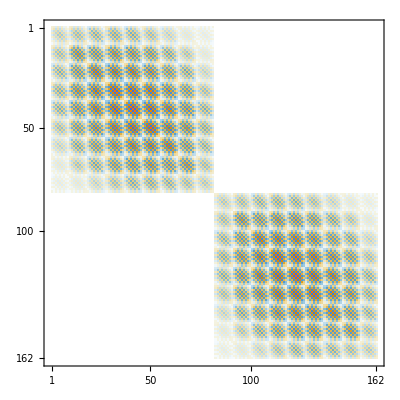

```mathematica
massQ//MatrixPlot
```

```mathematica
hh[x_] := {3x[[1]],1x[[2]],3x[[3]]}
```

```mathematica
hhh=RandomReal[{-1,1},{3,3}];
```

```mathematica
Eigenvalues[hhh]
```

{-0.418134+0.700572 ⅈ,-0.418134-0.700572 ⅈ,0.3604+0. ⅈ}

```mathematica
Eigenvalues[hhh,1,Method->{"Arnoldi"}]
```

{-0.418134+0.700572 ⅈ}

```mathematica
?Eigenvalues
```

Eigenvalues[m] gives a list of the eigenvalues of the square matrix m. 
Eigenvalues[{m,a}] gives the generalized eigenvalues of m with respect to a. 
Eigenvalues[m,k] gives the first k eigenvalues of m. 
Eigenvalues[{m,a},k] gives the first k generalized eigenvalues.

```mathematica
Eigenvalues[{massU,ConjugateTranspose[S].inverseMassQ.S}]
```

{∞,4.,4.,2.,1.,1.,0.8,0.8,0.5,0.444258,0.444258,0.399849,0.399849,0.307603,0.307603,0.249461,0.249461,0.234816,0.234816,0.222129,0.199655,0.199655,0.159755,0.159755,0.143157,0.143157,0.138211,0.138211,0.12523,0.12523,0.12473,0.108269,0.108269,0.0933692,0.0933692,0.0912395,0.0912395,0.0909589,0.0909589,0.0853959,0.0853959,0.0771539,0.0771539,0.0715786,0.0679402,0.0679402,0.0565116,0.0565116,0.0466846,0.0184006,0.0184006,0.0183163,0.0183163,0.0180681,0.0180681,0.0176688,0.0176688,0.0171366,0.0171366,0.0163049,0.0163049,0.0153713,0.0153713,0.0118218,0.0118218,0.011787,0.011787,0.0116837,0.0116837,0.0115154,0.0115154,0.011287,0.011287,0.0109201,0.0109201,0.0104933,0.0104933,0.0092003,0.0071976,0.0071976,0.00591092}

```mathematica
?Eigenvalues
```

RowBox[{"Eigenvalues", "[", StyleBox["m", "TI"], "]"}] gives a list of the eigenvalues of the square matrix StyleBox["m", "TI"]. 
RowBox[{"Eigenvalues", "[", RowBox[{"{", RowBox[{StyleBox["m", "TI"], ",", StyleBox["a", "TI"]}], "}"}], "]"}] gives the generalized eigenvalues of StyleBox["m", "TI"] with respect to StyleBox["a", "TI"]. 
RowBox[{"Eigenvalues", "[", RowBox[{StyleBox["m", "TI"], ",", StyleBox["k", "TI"]}], "]"}] gives the first StyleBox["k", "TI"] eigenvalues of StyleBox["m", "TI"]. 
RowBox[{"Eigenvalues", "[", RowBox[{RowBox[{"{", RowBox[{StyleBox["m", "TI"], ",", StyleBox["a", "TI"]}], "}"}], ",", StyleBox["k", "TI"]}], "]"}] gives the first StyleBox["k", "TI"] generalized eigenvalues.

```mathematica
hh[x_] := inverseMassU.(ℐ1-ConjugateTranspose[Γ].sInverse[Γ.inverseMassU.ConjugateTranspose[Γ]].Γ.inverseMassU).ConjugateTranspose[S].inverseMassQ.(ℐ2-ConjugateTranspose[Ξ].sInverse[Ξ.inverseMassQ.ConjugateTranspose[Ξ]].Ξ.inverseMassQ).S.x
```

```mathematica
Eigenvalues[hh]
```

Eigenvalues[hh]

```mathematica
?LinearSolve
```

LinearSolve[m,b] finds an x that solves the matrix equation m.x==b. 
LinearSolve[m] generates a LinearSolveFunction[…] that can be applied repeatedly to different b.

SparseArray[<78>, {32, 16}]

SparseArray[<8>, {32, 8}]

```mathematica
ℐ1=SparseArray@IdentityMatrix[Length[U]];
ℐ2=SparseArray@IdentityMatrix[Length[Q]];
```

```mathematica
ℐ
```

SparseArray[<16>, {16, 16}]

```mathematica
ConjugateTranspose[Γ].Γ
```

0.

```mathematica
inverseMassQ.(-S.uTildeNow-ConjugateTranspose[Ξ].μTildeNow)
```

-5.96856×10^-13

```mathematica
ℐ
```

SparseArray[<16>, {16, 16}]

```mathematica
inverseMassU.ConjugateTranspose[S].QTildeNow-inverseMassU.ConjugateTranspose[Γ].LinearSolve[Γ.inverseMassU.ConjugateTranspose[Γ],Γ.inverseMassU.ConjugateTranspose[S].QTildeNow]-inverseMassU.(ℐ-ConjugateTranspose[Γ].SparseArray[Inverse[Γ.inverseMassU.ConjugateTranspose[Γ]]].Γ.inverseMassU).ConjugateTranspose[S].QTildeNow
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
(ℐ-inverseMassU.ConjugateTranspose[Γ].SparseArray[Inverse[Γ.inverseMassU.ConjugateTranspose[Γ]]].Γ).(ℐ-inverseMassU.ConjugateTranspose[Γ].SparseArray[Inverse[Γ.inverseMassU.ConjugateTranspose[Γ]]].Γ)-(ℐ-inverseMassU.ConjugateTranspose[Γ].SparseArray[Inverse[Γ.inverseMassU.ConjugateTranspose[Γ]]].Γ)//
```

SparseArray[<0>, {400, 400}]

```mathematica
ℐ=SparseArray@IdentityMatrix[Length[ConjugateTranspose[S].QTildeNow]];
```

```mathematica
inverseMassU
```

```mathematica
(ℐ-inverseMassU.ConjugateTranspose[Γ].SparseArray[Inverse[Γ.inverseMassU.ConjugateTranspose[Γ]]].Γ).inverseMassU.ConjugateTranspose[S].QTildeNow//Chop
```

{0,-105.108,-105.99,11.8564,155.27,0,-0.478165,45.5998,-27.1383,-22.2043,0,-47.4835,-39.1385,14.1113,245.968,0,92.144,94.1978,-41.9415,-2.76013,0,-431.404,-373.137,123.288,-112.303,-93.2338,-39.845,101.389,-0.871394,182.508,47.8784,29.0411,-33.5876,44.0821,-137.008,-55.2744,-46.2443,35.5378,-18.8939,237.808,-30.5808,-12.7946,-16.1572,-89.5804,-40.835,162.94,203.098,248.911,416.39,107.213,0,148.606,154.946,-72.7056,-36.3075,0,34.3588,-9.69493,9.89415,193.444,0,-8.96195,35.3406,52.9869,-478.676,0,-1.49812,-149.816,36.8823,-12.4809,0,389.364,554.931,202.429,-1420.56,-39.7701,-135.094,-111.772,-296.375,-24.0209,-99.2642,-1.75237,65.6992,-71.3628,252.545,257.065,42.2432,41.6694,-148.551,606.422,51.4302,-91.577,-30.21,55.0576,91.4562,141.336,321.948,110.928,-145.79,-79.7329,-50.0544,-174.528,-4.71602,118.345,252.747,131.543,-9.5171,48.802,-54.7634,-6.52811,20.1652,-86.7517,89.2837,-87.4711,511.925,-67.3087,209.572,-46.6147,-120.054,305.793,529.471,-1089.5,195.174,452.335,390.356,-273.874,-77.1806,3.26601,-92.8108,0,71.4031,43.9325,-2.53291,6.53307,0,-162.253,-20.2969,-26.6666,-2.89015,0,-43.3779,-0.738324,29.3725,37.9816,0,-463.328,-174.416,34.5243,-211.357,0,-40.3776,498.032,-17.363,-272.121,-406.508,-271.213,39.0397,-64.8313,105.263,-416.602,-123.843,-122.221,34.4407,-47.6678,313.805,-146.035,127.2,15.4405,-12.7262,112.943,504.474,-381.713,154.757,-331.055,997.801,127.379,160.363,-236.093,55.4883,0,169.515,-38.9556,54.36,-3.38215,0,-166.533,16.1183,-39.7127,-48.7284,0,73.8069,-26.777,97.8542,5.83512,0,-796.829,84.5837,-540.557,-49.2181,0,0,-261.453,-215.78,-43.2218,82.0261,0,-42.4652,35.635,-33.7382,182.311,0,-15.5936,66.9554,-42.7605,194.427,0,-77.9404,34.572,-19.7062,23.5038,0,104.573,153.033,94.5626,-534.568,134.389,-84.4717,20.4757,59.6332,458.673,-69.8759,14.3209,-33.7149,-5.19292,-205.641,-118.32,-16.5998,41.4903,60.4857,-132.386,238.048,0.239678,-36.2139,-108.927,369.996,-518.591,-117.602,4.06151,590.637,-656.306,0,-60.5094,-167.364,11.3196,-92.2059,0,-2.04081,-25.5754,98.3118,-429.034,0,15.3852,-37.9233,109.902,-633.554,0,13.1708,-77.5928,77.2785,-470.38,0,-2.9858,4.91395,77.8486,-111.567,242.792,68.2192,26.5012,-102.111,-360.539,219.483,-18.0692,44.5612,-49.3887,167.524,193.714,35.7457,-67.5336,56.9228,-11.6192,75.4914,35.5994,-111.635,154.86,-799.311,-45.1561,-82.3337,80.2289,-65.0062,389.183,-527.62,-47.19,-101.782,171.18,-594.6,-50.0645,60.7586,-101.784,140.893,-588.096,87.2466,-34.302,25.3308,-68.9075,-41.7479,-225.856,54.8509,48.4984,-13.6126,19.3984,-306.285,-87.0095,-297.72,280.348,-698.274,214.747,-31.1283,207.528,123.468,0,200.441,-3.08622,-18.2624,27.99,0,9.4727,7.91716,-76.9398,83.2008,0,114.084,-13.8152,45.5613,-108.344,0,-407.555,53.2033,-244.691,617.184,0,374.987,24.0321,83.0956,-171.036,139.13,49.0192,-35.0787,47.1942,-51.7179,231.391,-214.893,6.54611,-24.0735,95.5376,-433.828,329.353,25.3893,-19.2795,-24.4976,169.888,-99.0633,-64.6997,55.2915,-55.1336,247.167,476.835,-45.5877,88.9176,-290.342,0,-73.5902,-12.0284,-6.68435,22.4209,0,137.832,-0.30194,-18.176,56.8876,0,4.06331,-9.32104,44.1811,-61.907,0,-125.268,-26.8221,-16.7669,63.1242,0}

```mathematica
Γ.(inverseMassU.(ConjugateTranspose[S].QTildeNow)-inverseMassU.(ConjugateTranspose[Γ].λTildeNow))//Chop
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
S.ConjugateTranspose[(NullSpace[Γ])]
```

{}

```mathematica
ArrayFlatten[
{
{},
{}
}
]
```